```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\蛋白质浓度测量\\UltraViolet.xlsx"]
```

```mathematica
data1={{0.,0.},{0.25,0.1395},{0.375,0.21},{0.5,0.2795},{0.625,0.349},{0.75,0.422},{1.,0.5634999999999999}}
```

```mathematica
{{0.,0.},{0.25,0.1395},{0.375,0.21},{0.5,0.2795},{0.625,0.349},{0.75,0.422},{1.,0.5634999999999999}}
lm1=LinearModelFit[data1,x,x]
```

{{0.,0.},{0.25,0.1395},{0.375,0.21},{0.5,0.2795},{0.625,0.349},{0.75,0.422},{1.,0.5635}}

FittedModel[-0.00121429+0.563429 x]

```mathematica
Normal[lm1]
```

-0.00121429+0.563429 x

```mathematica
Show[ListPlot[data1],Plot[lm1[x],{x,0,1}],AxesLabel-> {"protein concentration(mg/mL)","OD280"}]
```

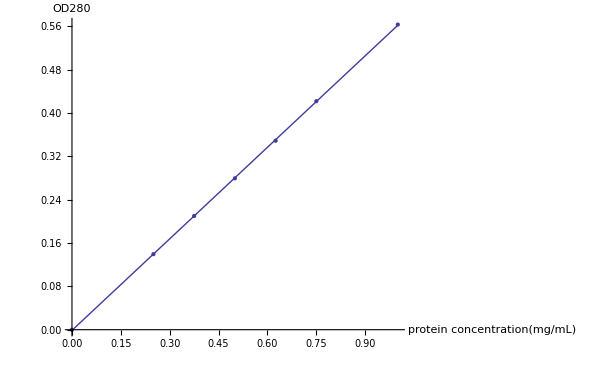

```mathematica
lm1["RSquared"]
```

0.99996